1. Задаем начальные данные :

```mathematica
X={π/6, π/4, π/3, π/2} 
f[x_]:=Cot[x]^2
F=f /@ X
```

{π/6,π/4,π/3,π/2}

{3,1,1/3,0}

```mathematica
n=Length[X]-1
```

3

```mathematica
Do[{Subscript[x, i]=X[[i+1]],Subscript[f, i]=F[[i+1]]},{i,0,n}]
```

2. Строим алгебраический интерполяционный многочлен:

```mathematica
koef=Solve[Table[Subscript[a, 0]+∑_(k=1)^n Subscript[a, k] Subscript[x, j]^k==Subscript[f, j],{j, 0, n}],{}][[1]]
```

{a_0→14,a_1→-103/π,a_2→258/π^2,a_3→-216/π^3}

```mathematica
P[x_]=∑_(k=0)^n Subscript[a, k] x^k//.koef
```

14-(103 x)/π+(258 x^2)/π^2-(216 x^3)/π^3

3. Строим интерполяционный многочлен с помощью встроенной функции InterpolatingPolynomial:

```mathematica
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}]
P1[x_]=InterpolatingPolynomial[Tb1,x]//Expand
```

{{π/6,3},{π/4,1},{π/3,1/3},{π/2,0}}

14-(103 x)/π+(258 x^2)/π^2-(216 x^3)/π^3

4. Сравниваем интерполяционные многочлены:

```mathematica
P[x]==P1[x]
```

True

5. Проверяем выполнение интерполяционных условий:

```mathematica
Table[P[Subscript[x, i]]==Subscript[f, i],{i,0,n}]
```

{True,True,True,True}

6. Изображаем исходную систему точек и полученный интерполяционный многочлен в одной системе координат:

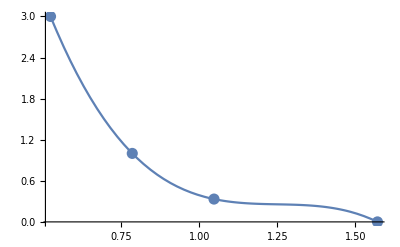

```mathematica
Gr1=ListPlot[Tb1,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

6. Найти приближенное значение при указанном аргументе и сравнить с точным значением функции:

```mathematica
asdP=P[π/5]//N
```

1.992

```mathematica
absP=Abs[asdP-f[π/5]]
```

0.0975728

```mathematica
dP=absP/asdP*100
```

4.89823